# Simulation on SMWDC ray - tracking

assume there are 6 planes XX' UU' VV’
each cells with size 20 mm X 16 mm
O’ planes are shifted by 5mm
a particle pass throught the MWDC and created signal
	signal constains : 
 	1) # of wire hitted
 	2) hitted wire ID
 	3) the Leading edge of the signal
 by using the drift velocity, we can reconstruct the particle ray.
 the origin of the cooredinate is

```mathematica
(* have to rotate the UU' and VV' plan *)
```

```mathematica
(* initial *)
a=1;
Clear[a];
```

## Raw Signal Generation

```mathematica
(* a paricle's travaling path *)
 (* particle start position *)
Pstart[x_,y_]:={x,y, 0};
 (* particle end position *)
Pend[x_,y_]:={x,y, 16*5};
(* particle ray *) (* k ={x0, y0, x1, y1} *)
Pray[k_,z_]:=N[(Pend[k[[3]],k[[4]]]-Pstart[k[[1]],k[[2]]])z/(16*5)+Pstart[k[[1]],k[[2]]]]
(* Para = {a, x0, b, y0}*)
Para[k_]:={(k[[3]]-k[[1]])/(5*16),k[[1]],(k[[4]]-k[[2]])/(5*16),k[[2]]}//N
(* Tools *)
RotzRH[θ_]:={{Cos[θ],-Sin[θ],0},{Sin[θ],Cos[θ],0},{0,0,1}}
DirPray[k_]:=Normalize[{k[[3]]-k[[1]],k[[4]]-k[[2]],16*5}]
AngPray[k_]:={Arg[DirPray[k][[3]]+ⅈ √((DirPray[k][[2]])^2  +(DirPray[k][[1]])^2) ] 180/π//N,Arg[DirPray[k][[1]]+ⅈ DirPray[k][[2]]] 180/π}
RGB[θ_]:=If[0≤ θ<120,RGBColor[Cos[θ/120 π/2],Sin[θ/120 π/2],0],
If[120≤ θ<240,RGBColor[0,Cos[(θ-120)/120 π/2],Sin[(θ-120)/120 π/2]],
If[240≤ θ<360,RGBColor[Sin[(θ-240)/120 π/2],0,Cos[(θ-240)/120 π/2]],0],0],0]
(* wire direction *)
wnorm[plan_]:=Switch[plan,
1, {0,1,0},
2,{0,1,0},
3,{-0.6,0.8,0},
4,{-0.6,0.8,0},
5,{0.6,0.8,0},
6,{0.6,0.8,0}
]
cell(*X,Z,Y*)={20,400,16};
firstwirePosition={0,5,18.1225,11.8725,18.1225,11.8725};
wstart[plan_,i_]:=
{(i-1)cell[[1]]/(wnorm[plan][[2]])+firstwirePosition[[plan]],0,cell[[3]](plan-1)}
(* wire *)
w[plan_,i_,s_]:=wstart[plan,i]+s wnorm[plan]
(* chamber geometery *)
MWDC[k_,XYZ_, size_, α_]:=Graphics3D[{
J=HitList[k];
{Black,Arrow[{{0,0,0},{0,0,100}}]},
{Black,Arrow[{{0,0,0},{1120,0,0}}]},
{Black,Arrow[{{0,0,0},{0,250,0}}]},
{Red,Arrow[{Pray[k,-30],Pray[k,100]}]},
Table[{Green,Opacity[Highlight[1,i,J]],EdgeForm[Opacity[α]],Cuboid[wstart[1,i]+1/2 cell,wstart[1,i]-1/2 cell]},{i,1,56}],
Table[{Green,Opacity[Highlight[2,i,J]],EdgeForm[Opacity[α]],Cuboid[wstart[2,i]+1/2 cell,wstart[2,i]-1/2 cell]},{i,1,56}],
Table[{Yellow,Opacity[Highlight[3,i,J]],EdgeForm[Opacity[α]],Rotate[Cuboid[wstart[3,i]+1/2 cell,wstart[3,i]-1/2 cell],-ArcSin[wnorm[3][[1]]],{0,0,1},wstart[3,i]]},{i,1,44}],
Table[{Yellow,Opacity[Highlight[4,i,J]],EdgeForm[Opacity[α]],Rotate[Cuboid[wstart[4,i]+1/2 cell,wstart[4,i]-1/2 cell],-ArcSin[wnorm[4][[1]]],{0,0,1},wstart[4,i]]},{i,1,44}],
Table[{Blue,Opacity[Highlight[5,i,J]],EdgeForm[Opacity[α]],Rotate[Cuboid[wstart[5,i]+1/2 cell,wstart[5,i]-1/2 cell],-ArcSin[wnorm[5][[1]]],{0,0,1},wstart[5,i]]},{i,1,44}],
Table[{Blue,Opacity[Highlight[6,i,J]],EdgeForm[Opacity[α]],Rotate[Cuboid[wstart[6,i]+1/2 cell,wstart[6,i]-1/2 cell],-ArcSin[wnorm[6][[1]]],{0,0,1},wstart[6,i]]},{i,1,44}]
}, ImageSize->size, PlotRange->XYZ]
MWDC2[k_, size_, α_]:=Graphics3D[{
J=HitList[k];
fp=FirstPlan[J];
Ymin=Min[Pray[k,-10][[2]],Pray[k,100][[2]]]-20;
Ymax=Max[Pray[k,-10][[2]],Pray[k,100][[2]]]+20;
Corner1[plan_]:={-cell[[1]]/2,Ymin/(wnorm[plan][[2]]),-cell[[3]]/2};
Corner2[plan_]:={cell[[1]]/2,Ymax/(wnorm[plan][[2]]),cell[[3]]/2};
(*Z*){Black,Arrow[{w[J[[1,1]],J[[1,2]],0],w[J[[1,1]],J[[1,2]],0]+{0,0,100}}]},
(*X*){Black,Arrow[{w[J[[1,1]],J[[1,2]],0],w[J[[1,1]],J[[1,2]],0]+{40,0,0}}]},
(*Y*){Black,Arrow[{w[J[[1,1]],J[[1,2]],0],w[J[[1,1]],J[[1,2]],0]+{0,Pray[k,100][[2]]+50,0}}]},
{Red,Thickness[Large ],Arrow[{Pray[k,-30],Pray[k,100]}]},
Table[{Green,Opacity[Highlight[1,i,J]],EdgeForm[Opacity[α]],Cuboid[wstart[1,i]+Corner1[1],wstart[1,i]+Corner2[1]]},{i,J[[1,2]]-2,J[[1,2]]+2}],
Table[{Green,Opacity[Highlight[2,i,J]],,EdgeForm[Opacity[α]],Cuboid[wstart[2,i]+Corner1[2],wstart[2,i]+Corner2[2]]},{i,J[[fp[[2]],2]]-2,J[[fp[[2]],2]]+2}],
Table[{Yellow,Opacity[Highlight[3,i,J]],,EdgeForm[Opacity[α]],Rotate[Cuboid[wstart[3,i]+Corner1[3],wstart[3,i]+Corner2[3]],-ArcSin[wnorm[3][[1]]],{0,0,1},wstart[3,i]]},{i,J[[fp[[3]],2]]-2,J[[fp[[3]],2]]+2}],
Table[{Yellow,Opacity[Highlight[4,i,J]],,EdgeForm[Opacity[α]],Rotate[Cuboid[wstart[4,i]+Corner1[4],wstart[4,i]+Corner2[4]],-ArcSin[wnorm[4][[1]]],{0,0,1},wstart[4,i]]},{i,J[[fp[[4]],2]]-2,J[[fp[[4]],2]]+2}],
Table[{Blue,Opacity[Highlight[5,i,J]],,EdgeForm[Opacity[α]],Rotate[Cuboid[wstart[5,i]+Corner1[5],wstart[5,i]+Corner2[5]],-ArcSin[wnorm[5][[1]]],{0,0,1},wstart[5,i]]},{i,J[[fp[[5]],2]]-2,J[[fp[[5]],2]]+2}],
Table[{Blue,Opacity[Highlight[6,i,J]],,EdgeForm[Opacity[α]],Rotate[Cuboid[wstart[6,i]+Corner1[6],wstart[6,i]+Corner2[6]],-ArcSin[wnorm[6][[1]]],{0,0,1},wstart[6,i]]},{i,J[[fp[[6]],2]]-2,J[[fp[[6]],2]]+2}],
Table[{Red,Opacity[0.5],Cylinder[{w[J[[i,1]],J[[i,2]],Ymin-20],w[J[[i,1]],J[[i,2]],Ymax+20]},J[[i,6]]]},{i,1,Length[J]}],
Text[J[[1,2]],w[J[[1,1]],J[[1,2]],0]+{-10,0,0}]
}, ImageSize->size]
MWDC3[k1_,k2_, size_, α_,plan_]:=ImageReflect[Graphics[{
J1=HitList[k1];
J2=HitList[k2];
fp1=FirstPlan[J1];
fp2=FirstPlan[J2];
(*Z*){Black,Arrow[{Drop[w[J1[[plan,1]],J1[[plan,2]],0],{2}],Drop[w[J1[[plan,1]],J1[[plan,2]],0],{2}]+{0,30}}]},
(*X*){Black,Arrow[{Drop[w[J1[[plan,1]],J1[[plan,2]],0],{2}],Drop[w[J1[[plan,1]],J1[[plan,2]],0],{2}]+{30,0}}]},
{Red,Thickness[Large ],Arrow[{Drop[Pray[k1,-10],{2}],Drop[Pray[k1,30],{2}]}]},
{Blue,Thickness[Large ],Arrow[{Drop[Pray[k2,-10],{2}],Drop[Pray[k2,30],{2}]}]},
Table[{Green,Opacity[0.2],EdgeForm[Opacity[α]],Rectangle[Drop[wstart[plan,i]-1/2 cell/{wnorm[plan][[2]],1,1},{2}],Drop[wstart[plan,i]+1/2 cell/{wnorm[plan][[2]],1,1},{2}]]},{i,J1[[fp1[[plan]],2]],J1[[fp1[[plan]],2]]+2}],
Table[{Green,Opacity[0.2],,EdgeForm[Opacity[α]],Rectangle[Drop[wstart[plan+1,i]-1/2 cell/{wnorm[plan+1][[2]],1,1},{2}],Drop[wstart[plan+1,i]+1/2 cell/{wnorm[plan+1][[2]],1,1},{2}]]},{i,J1[[fp1[[plan+1]],2]],J1[[fp1[[plan+1]],2]]+2}],
Table[{Red,
Circle[Drop[w[J1[[i,1]],J1[[i,2]],0],{2}],{J1[[i,6]]/(wnorm[plan][[2]]),J1[[i,6]]}]},{i,fp1[[plan]],fp1[[plan+1]]}],
Table[{Blue,
Circle[Drop[w[J2[[i,1]],J2[[i,2]],0],{2}],{J2[[i,6]]/(wnorm[plan][[2]]),J2[[i,6]]}]},{i,fp2[[plan]],fp2[[plan+1]]}],
Text[J1[[1,2]],Drop[w[J1[[1,1]],J1[[1,2]],0]+{-5,0,0},{2}]]
}, ImageSize->size],Left->Right]
```

```mathematica
MWDC2[{189,10,100,10},500,0.5]
J//TableForm
```

-Graphics3D-

1 | 10 | 0 | 10. | 4.47455 | 6.01653
1 | 11 | 0 | 10. | -5.46889 | 7.35353
2 | 9 | 16 | 10. | 19.0825 | 4.14472
2 | 10 | 16 | 10. | 9.13903 | 9.22534
3 | 7 | 32 | 14.9181 | 29.1305 | 4.31615
4 | 6 | 48 | 10.415 | 50.4742 | 3.72154
5 | 5 | 64 | 9.88101 | 60.8921 | 4.67471
6 | 4 | 80 | 14.3841 | 82.2358 | 3.36298

## Signal Construction

```mathematica
(* the wire coodinate integer *)
(* a shortest distance between 2 lines*) 
MaxDriftLen[plan_]:=Switch[plan,
1,10,
2,10,
3,10,
4,10,
5,10,
6,10
]
DriftLen[k_,plan_,i_]:={s,z,dl}/.Flatten[Solve[w[plan,i,s]+dl Normalize[Cross[wnorm[plan],DirPray[k]]]==Pray[k,z],{s,z,dl}]]
HitList[k_]:=
Flatten[
DeleteCases[
Table[If[Abs[DriftLen[k,plan,i][[3]]]<MaxDriftLen[plan],{plan,i,(plan-1)*16,DriftLen[k,plan,i][[1]],DriftLen[k,plan,i][[2]],Abs[DriftLen[k,plan,i][[3]]]},0],{plan,1,6},{i,1,56}]
,0,2]
,1]
FirstPlan[Lis_]:=Flatten[Table[Position[Lis,{i,__}][[1]],{i,1,6}]];
Highlight[plane_,wire_,lis_]:=If[MemberQ[lis,{plane,wire,__}],0.5,0.1]
```

```mathematica
MWDC[k,All,1000,0.5]
```

-Graphics3D-

```mathematica
k=PayOnMWDC[1,30];
AngPray[k]
HitList[k]//TableForm
MWDC2[k,800,0.1]
```

{30.,180.}

1 | 8 | 0 | 0. | -2.35142 | 4.70284
2 | 7 | 16 | 0. | 16.1438 | 0.287537
3 | 5 | 32 | 1.0029 | 31.3824 | 1.47294
4 | 5 | 48 | 2.48029 | 46.4725 | 3.64276
5 | 4 | 64 | 2.22365 | 65.3694 | 3.26584
6 | 4 | 80 | 0.746259 | 80.4596 | 1.09602

-Graphics3D-

```mathematica
AngPray[k]
HitList[k]//TableForm
MWDC[k,{{Min[k[[1]],k[[3]]]-20,Max[k[[1]],k[[3]]]+20},{Min[k[[2]],k[[4]]]-5,Max[k[[2]],k[[4]]]+5},All},500,0.3]
```

{30.,180.}

1 | 8 | 0 | 0. | -2.35142 | 4.70284
2 | 7 | 16 | 0. | 16.1438 | 0.287537
3 | 5 | 32 | 1.0029 | 31.3824 | 1.47294
4 | 5 | 48 | 2.48029 | 46.4725 | 3.64276
5 | 4 | 64 | 2.22365 | 65.3694 | 3.26584
6 | 4 | 80 | 0.746259 | 80.4596 | 1.09602

-Graphics3D-

### Alternative For Minimum

```mathematica
SZ[plan_,i_,k_]:=Inverse[{{-1,wnorm[plan].(Pray[k,1]-Pray[k,0])},{-wnorm[plan].(Pray[k,1]-Pray[k,0]),Norm[(Pray[k,1]-Pray[k,0])]^2}}].{(wstart[plan,i]-Pray[k,0]).wnorm[plan],(wstart[plan,i]-Pray[k,0]).(Pray[k,1]-Pray[k,0])}
DL[plan_,i_,k_]:=Norm[Pray[k,SZ[plan,i,k][[2]]]-w[plan,i,SZ[plan,i,k][[1]]]]
SZD[plan_,i_,k_]:=Flatten[{SZ[plan,i,k],DL[plan,i,k]}]
HitListSZD[k_]:=
Flatten[
DeleteCases[
Table[If[Abs[SZD[plan,i,k][[3]]]<MaxDriftLen[plan],{plan,i,(plan-1)*16,SZD[plan,i,k][[1]],SZD[plan,i,k][[2]],Abs[SZD[plan,i,k][[3]]]},0],{plan,1,6},{i,1,56}]
,0,2]
,1]
```

```mathematica
DriftLen2[k_,plan_,i_]:=Flatten[{{s,z}/.FindMinimum[Norm[w[plan,i,s]-Pray[k,z]],{s,-200,200},{z,-10,90}][[2]],FindMinimum[Norm[w[plan,i,s]-Pray[k,z]],{s,-200,200},{z,-10,90}][[1]]}]
HitList2[k_]:=
Flatten[
DeleteCases[
Table[If[Abs[DriftLen2[k,plan,i][[3]]]<MaxDriftLen[plan],{plan,i,(plan-1)*16,DriftLen2[k,plan,i][[1]],DriftLen2[k,plan,i][[2]],Abs[DriftLen2[k,plan,i][[3]]]},0],{plan,1,6},{i,1,56}]
,0,2]
,1]
```

```mathematica
Timing[HitList[k]//TableForm]
Timing[HitList2[k]//TableForm]
Timing[HitListSZD[k]//TableForm]
```

{0.624,1 | 26 | 0 | 67.4328 | 1.31629 | 7.0832
2 | 26 | 16 | 67.1896 | 15.8508 | 0.803031
3 | 23 | 32 | 82.8583 | 32.1693 | 1.06316
4 | 23 | 48 | 88.0904 | 46.9771 | 6.42155
5 | 19 | 64 | 80.2355 | 63.4811 | 3.70963
6 | 18 | 80 | 89.2318 | 81.2455 | 8.905}

{2.371,1 | 26 | 0 | 67.4328 | 1.31629 | 7.0832
2 | 26 | 16 | 67.1896 | 15.8508 | 0.803031
3 | 23 | 32 | 82.8583 | 32.1693 | 1.06316
4 | 23 | 48 | 88.0904 | 46.9771 | 6.42155
5 | 19 | 64 | 80.2355 | 63.4811 | 3.70963
6 | 18 | 80 | 89.2318 | 81.2455 | 8.905}

{1.295,1 | 26 | 0 | 67.4328 | 1.31629 | 7.0832
2 | 26 | 16 | 67.1896 | 15.8508 | 0.803031
3 | 23 | 32 | 82.8583 | 32.1693 | 1.06316
4 | 23 | 48 | 88.0904 | 46.9771 | 6.42155
5 | 19 | 64 | 80.2355 | 63.4811 | 3.70963
6 | 18 | 80 | 89.2318 | 81.2455 | 8.905}

## ReConstruction 2 - Multi - Demension Regession

```mathematica
h[z1_,z2_,z3_,z4_,z5_,z6_]:={
{z1,1,0,0},
{z2,1,0,0},
{0.8z3 , 0.8,-0.6 z3 ,-0.6},
{0.8z4 , 0.8, -0.6z4 ,-0.6},
{0.8z5, 0.8, 0.6z5 ,0.6},
{0.8z6, 0.8, 0.6z6 ,0.6}
}
hh=h[0,16,32,48,64,80];
hh2=h[-40,-24,-8,8,24,40];
(* Hit List Function *)
InputDist[J_]:=Table[{
firstwirePosition[[J[[FirstPlan[J][[i]],1]]]]wnorm[FirstPlan[J][[i]]][[2]]+
(J[[FirstPlan[J][[i]],2]]-1)cell[[1]]-Transpose[J][[6,FirstPlan[J][[i]]]],firstwirePosition[[J[[FirstPlan[J][[i]],1]]]]wnorm[FirstPlan[J][[i]]][[2]]+(J[[FirstPlan[J][[i]],2]]-1)cell[[1]]+Transpose[J][[6,FirstPlan[J][[i]]]]},
{i,1,Length[FirstPlan[J]]}]
```

```mathematica
(* The normal equation = least square equation *)
(* Transpose[hh].hh. B == Transpose[hh].Y *)
```

```mathematica
MWDC2[PayOnMWDC[1,40],500,0.1]
```

-Graphics3D-

```mathematica
J=HitList[PayOnMWDC[1,40]];
J//TableForm
```

1 | 23 | 0 | 0. | -2.1528 | 6.29437
2 | 22 | 16 | 0. | 16.7965 | 2.3287
3 | 17 | 32 | -1.95364 | 32.7585 | 2.71303
4 | 17 | 48 | -2.18952 | 48.85 | 3.04061
5 | 17 | 64 | -4.48841 | 62.2574 | 6.23308
6 | 17 | 80 | -4.25252 | 78.349 | 5.90551

```mathematica
MWDC2[k,500,0.1]
```

-Graphics3D-

```mathematica
Transpose[(Transpose[hh].hh)]//MatrixForm
Inverse[Transpose[(Transpose[hh].hh)]]//MatrixForm
Transpose[hh].{X1,X2,V1,V2,U1,U2}//MatrixForm
```

```mathematica
({{9103.36, 159.36, 3440.64, 30.71999999999999}, {159.36, 4.5600000000000005, 30.720000000000006, 0.}, {3440.64, 30.720000000000006, 4976.639999999999, 80.63999999999999}, {30.71999999999999, 0., 80.63999999999999, 1.44}})
```

(0.000812315 | -0.0144457 | -0.00206959 | 0.0985677
-0.0144457 | 0.654984 | 0.0102652 | -0.266674
-0.00206959 | 0.0102652 | 0.00921227 | -0.471736
0.0985677 | -0.266674 | -0.471736 | 25.0089)

(51.2 U1+64. U2+25.6 V1+38.4 V2+16 X2
0.8 U1+0.8 U2+0.8 V1+0.8 V2+X1+X2
38.4 U1+48. U2-19.2 V1-28.8 V2
0.6 U1+0.6 U2-0.6 V1-0.6 V2)

```mathematica
Transpose[(Transpose[hh2].hh2)]//MatrixForm
Inverse[Transpose[(Transpose[hh2].hh2)]]//MatrixForm
Transpose[hh2].{X1,X2,V1,V2,U1,U2}//MatrixForm
```

(3650.56 | -23.04 | 983.04 | 30.72
-23.04 | 4.56 | 30.72 | 0.
983.04 | 30.72 | 829.44 | 23.04
30.72 | 0. | 23.04 | 1.44)

(0.000812315 | 0.0180468 | -0.00206959 | 0.0157841
0.0180468 | 0.799028 | -0.0725185 | 0.775296
-0.00206959 | -0.0725185 | 0.00921227 | -0.103245
0.0157841 | 0.775296 | -0.103245 | 2.00964)

(19.2 U1+32. U2-6.4 V1+6.4 V2-40 X1-24 X2
0.8 U1+0.8 U2+0.8 V1+0.8 V2+X1+X2
14.4 U1+24. U2+4.8 V1-4.8 V2
0.6 U1+0.6 U2-0.6 V1-0.6 V2)

```mathematica
hh2//TableForm
```

-40 | 1 | 0 | 0
-24 | 1 | 0 | 0
-6.4 | 0.8 | 4.8 | -0.6
6.4 | 0.8 | -4.8 | -0.6
19.2 | 0.8 | 14.4 | 0.6
32. | 0.8 | 24. | 0.6

```mathematica
(*k=PayOnMWDC[1,20];*)
k={400, -120, 350, -120};
Para[k]
J=HitList[k];
J//TableForm
K=InputDist[J];
PosiYList=Flatten[Table[
{x1,x2,u3,u4,y5,y6},
{x1,{K[[1,1]],K[[1,2]]}},
{x2,{K[[2,1]],K[[2,2]]}},
{u3,{K[[3,1]],K[[3,2]]}},
{u4,{K[[4,1]],K[[4,2]]}},
{y5,{K[[5,1]],K[[5,2]]}},
{y6,{K[[6,1]],K[[6,2]]}}
],5];
SSError=Table[{i,LinearModelFit[{hh2,PosiYList[[i]]}]["ANOVATableEntries"][[-2,2]]},{i,1,64}];
SortedSSError=Sort[SSError,#1[[2]]<#2[[2]]&];
PosiYList[[SortedSSError[[1,1]]]]
LinearModelFit[{hh2,PosiYList[[SortedSSError[[1,1]]]]},{a,x0,b,y0}]["ParameterTable"]
LinearModelFit[{hh2,PosiYList[[SortedSSError[[1,1]]]]},{a,x0,b,y0}]["ParameterConfidenceIntervalTable"]
LinearModelFit[{hh2,PosiYList[[SortedSSError[[1,1]]]]},{a,x0,b,y0}]["ANOVATable"]
Estβ=LinearModelFit[{hh2,PosiYList[[SortedSSError[[1,1]]]]},{a,x0,b,y0}][{"BestFitParameters","ParameterErrors"}]
Para[k]-Estβ[[1]]
```

{-0.625,400.,0.,-120.}

1 | 21 | 0 | -120. | 0. | 0.
2 | 20 | 16 | -120. | 18.2472 | 4.23999
3 | 12 | 32 | -148.501 | 31.0008 | 2.23428
4 | 12 | 48 | -146.701 | 45.8008 | 4.91756
5 | 18 | 64 | -146.699 | 66.2008 | 4.92114
6 | 18 | 80 | -148.499 | 81.0008 | 2.23786

{400.,389.24,232.264,224.58,359.419,351.736}

| Estimate | Standard Error | t-Statistic | P-Value
a | -0.62061 | 0.0131256 | -47.2823 | 0.000447004
x0 | 374.795 | 0.41166 | 910.447 | 1.2064×10^-6
b | 0.00897146 | 0.0442019 | 0.202965 | 0.857937
y0 | 119.059 | 0.652855 | 182.367 | 0.000030067

| Estimate | Standard Error | Confidence Interval
a | -0.62061 | 0.0131256 | {-0.677085,-0.564135}
x0 | 374.795 | 0.41166 | {373.024,376.566}
b | 0.00897146 | 0.0442019 | {-0.181214,0.199157}
y0 | 119.059 | 0.652855 | {116.25,121.868}

| DF | SS | MS | F-Statistic | P-Value
a | 1 | 14337.1 | 14337.1 | 67599.9 | 0.0000147926
x0 | 1 | 637798. | 637798. | 3.00724×10^6 | 3.32531×10^-7
b | 1 | 9601.49 | 9601.49 | 45271.3 | 0.0000220883
y0 | 1 | 7053.53 | 7053.53 | 33257.6 | 0.000030067
Error | 2 | 0.424176 | 0.212088 |  | 
Total | 6 | 668791. |  |  |

{{-0.62061,374.795,0.00897146,119.059},{0.0131256,0.41166,0.0442019,0.652855}}

{-0.00438996,25.2051,-0.00897146,-239.059}

```mathematica
Needs["HypothesisTesting`"]
NormalPValue[1.96,TwoSided->True]
```

TwoSidedPValue→0.0499958

```mathematica
StudentTPValue[8.984,2,TwoSided->True]
```

TwoSidedPValue→0.0121641

```mathematica
StudentTCI[0,1,2]
```

{-4.30265,4.30265}

```mathematica
4.302*0.01313+-0.62061
```

-0.564125

```mathematica
(* random error *)
(* Ray Generation *)
Error=Module[
{k,J,K,PosiYList,SSError,SortedSSError},
Monitor[Table[
k=PayOnMWDC[1,θ];
(*AngPray[k];*)
J=HitList[k];
K=InputDist[J];
PosiYList=Flatten[Table[
{x1,x2,u3,u4,y5,y6},
{x1,{K[[1,1]],K[[1,2]]}},
{x2,{K[[2,1]],K[[2,2]]}},
{u3,{K[[3,1]],K[[3,2]]}},
{u4,{K[[4,1]],K[[4,2]]}},
{y5,{K[[5,1]],K[[5,2]]}},
{y6,{K[[6,1]],K[[6,2]]}}
],5];
SSError=Table[{i,LinearModelFit[{hh,PosiYList[[i]]}]["ANOVATableEntries"][[-2,2]]},{i,1,64}];
SortedSSError=Sort[SSError,#1[[2]]<#2[[2]]&];
(*LinearModelFit[{hh,PosiYM[[SortedSSError[[1,1]]]]},{a,x0,b,y0}]["ParameterConfidenceIntervalTable"];*)
(*LinearModelFit[{hh,PosiYM[[SortedSSError[[1,1]]]]},{a,x0,b,y0}][{"BestFitParameters","ParameterErrors"}]*)
Flatten[{θ,LinearModelFit[{hh,PosiYList[[SortedSSError[[1,1]]]]},{a,x0,b,y0}]["ParameterErrors"]}]
,{θ,20,70,0.1}],θ]
];
```

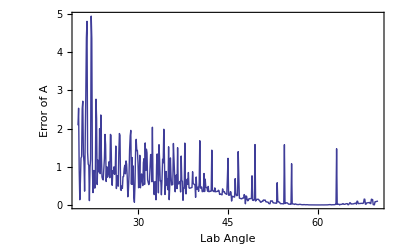

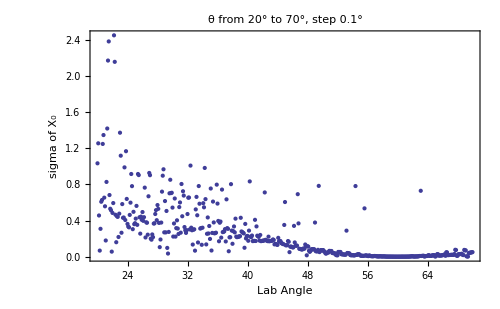

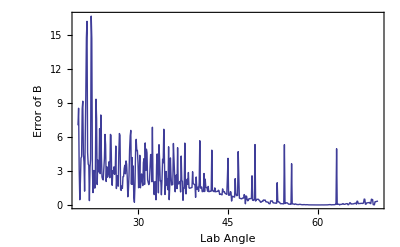

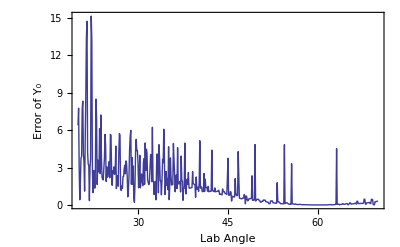

```mathematica
ListPlot[Table[{Error[[i,1]],Error[[i,2]] 180/π},{i,1,Length[Error]}],Joined->True,PlotRange->All,Frame->True,FrameLabel-> {"Lab Angle","Error of A"}]
ListPlot[Table[{Error[[i,1]],Error[[i,3]]},{i,1,Length[Error]}],(*Joined->True,*)PlotRange->All,Frame->True,FrameLabel-> {"Lab Angle","sigma of X_0"},PlotLabel-> "θ from 20° to 70°, step 0.1°",ImageSize-> 500]
ListPlot[Table[{Error[[i,1]],Error[[i,4]] 180/π},{i,1,Length[Error]}],Joined->True,PlotRange->All,Frame->True,FrameLabel-> {"Lab Angle","Error of B"}]
ListPlot[Table[{Error[[i,1]],Error[[i,5]]},{i,1,Length[Error]}],Joined->True,PlotRange->All,Frame->True,FrameLabel-> {"Lab Angle","Error of Y_0"}]
```

```mathematica
ModelError=Module[
{k,J,K,PosiYList,SSError,SortedSSError},
Monitor[Table[
k=PayOnMWDC[1,θ];
(*AngPray[k];*)
J=HitList[k];
K=InputDist[J];
PosiYList=Flatten[Table[
{x1,x2,u3,u4,y5,y6},
{x1,{K[[1,1]],K[[1,2]]}},
{x2,{K[[2,1]],K[[2,2]]}},
{u3,{K[[3,1]],K[[3,2]]}},
{u4,{K[[4,1]],K[[4,2]]}},
{y5,{K[[5,1]],K[[5,2]]}},
{y6,{K[[6,1]],K[[6,2]]}}
],5];
SSError=Table[{i,LinearModelFit[{hh,PosiYList[[i]]}]["ANOVATableEntries"][[-2,2]]},{i,1,64}];
SortedSSError=Sort[SSError,#1[[2]]<#2[[2]]&];
(*LinearModelFit[{hh,PosiYM[[SortedSSError[[1,1]]]]},{a,x0,b,y0}]["ParameterConfidenceIntervalTable"];*)
(*LinearModelFit[{hh,PosiYM[[SortedSSError[[1,1]]]]},{a,x0,b,y0}][{"BestFitParameters","ParameterErrors"}]*)
Flatten[{θ,LinearModelFit[{hh,PosiYList[[SortedSSError[[1,1]]]]},{a,x0,b,y0}]["BestFitParameters"],Para[k]}]
,{θ,20,70,0.1}],θ]
];
```

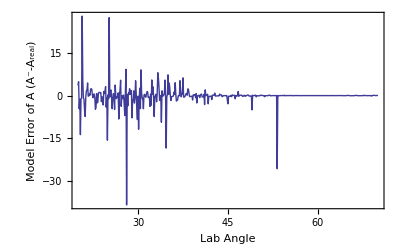

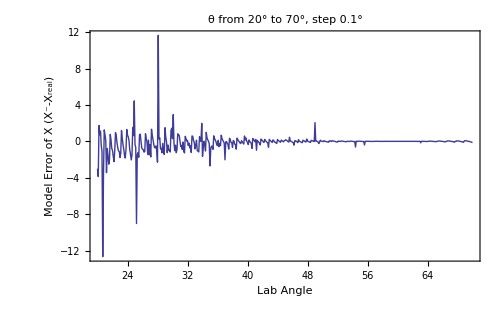

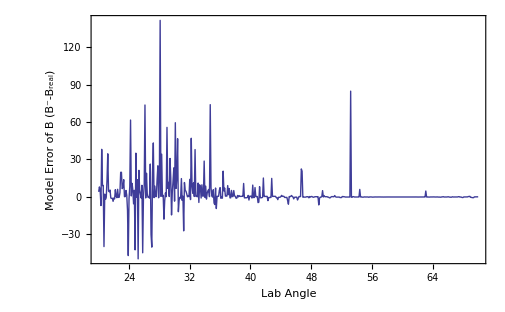

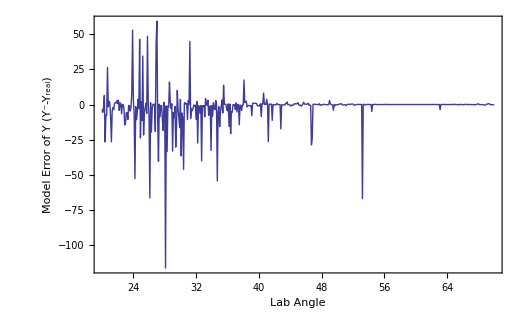

```mathematica
ListPlot[Table[{ModelError[[i,1]],(ModelError[[i,2]]-ModelError[[i,6]])180/π},{i,1,Length[ModelError]}],Joined->True,PlotRange->All,Frame->True,FrameLabel-> {"Lab Angle","Model Error of A (A^--A_real)"}]
ListPlot[Table[{ModelError[[i,1]],ModelError[[i,3]]-ModelError[[i,7]]},{i,1,Length[ModelError]}],Joined->True,PlotRange->All,Frame->True,FrameLabel-> {"Lab Angle","Model Error of X (X^--X_real)"},PlotLabel-> "θ from 20° to 70°, step 0.1°",ImageSize-> 500]
ListPlot[Table[{ModelError[[i,1]],(ModelError[[i,4]]-ModelError[[i,8]])180/π},{i,1,Length[ModelError]}],Joined->True,PlotRange->All,Frame->True,FrameLabel-> {"Lab Angle","Model Error of B (B^--B_real)"}]
ListPlot[Table[{ModelError[[i,1]],ModelError[[i,5]]-ModelError[[i,9]]},{i,1,Length[ModelError]}],Joined->True,PlotRange->All,Frame->True,FrameLabel-> {"Lab Angle","Model Error of Y (Y^--Y_real)"}]
```

```mathematica
ModelError[[1]]
```

{20.,-0.776712,145.33,0.0718202,-3.48343,-0.8391,148.342,0.,0.}

### Example for MWDC-L

```mathematica
Convertk[enck_]:=
{enck[[1]]+942.86-enck[[2]]40,enck[[3]]-enck[[4]]40,enck[[1]]+942.86+enck[[2]]40,enck[[3]]+enck[[4]]40}
```

```mathematica
GenPossRay[set_]:=Flatten[Table[{x1,x2,u1,u2,v1,v2},{x1,{wstart[set[[1,1]],set[[1,2]]][[1]] wnorm[1][[2]]-set[[1,4]],wstart[set[[1,1]],set[[1,2]]][[1]] wnorm[1][[2]]+set[[1,4]]}},{x2,{wstart[set[[2,1]],set[[2,2]]][[1]] wnorm[2][[2]]-set[[2,4]],wstart[set[[2,1]],set[[2,2]]][[1]] wnorm[2][[2]]+set[[2,4]]}},{u1,{wstart[set[[3,1]],set[[3,2]]][[1]] wnorm[3][[2]]-set[[3,4]],wstart[set[[3,1]],set[[3,2]]][[1]] wnorm[3][[2]]+set[[3,4]]}},{u2,{wstart[set[[4,1]],set[[4,2]]][[1]] wnorm[4][[2]]-set[[4,4]],wstart[set[[4,1]],set[[4,2]]][[1]] wnorm[4][[2]]+set[[4,4]]}},{v1,{wstart[set[[5,1]],set[[5,2]]][[1]] wnorm[5][[2]]-set[[5,4]],wstart[set[[5,1]],set[[5,2]]][[1]] wnorm[5][[2]]+set[[5,4]]}},{v2,{wstart[set[[6,1]],set[[6,2]]][[1]] wnorm[6][[2]]-set[[6,4]],wstart[set[[6,1]],set[[6,2]]][[1]] wnorm[6][[2]]+set[[6,4]]}}],5]
```

```mathematica
set={
{1,46.,117.82843,0.738441825},
{2,46.,124.799858,5.21638441},
{3,33.,121.574409,6.56764841},
{4,33.,109.076324,0.444934368},
{5,40.,134.319519,6.13150454},
{6,41.,105.490295,7.66625357}};
Rayset=GenPossRay[set];
SSError=Table[{i,LinearModelFit[{hh,Rayset[[i]]}]["ANOVATableEntries"][[-2,2]]},{i,1,64}];
SortedSSError=Sort[SSError,#1[[2]]<#2[[2]]&];
(*LinearModelFit[{hh,PosiYM[[SortedSSError[[1,1]]]]},{a,x0,b,y0}]["ParameterConfidenceIntervalTable"];*)
LinearModelFit[{hh,Rayset[[SortedSSError[[1,1]]]]},{a,x0,b,y0}]["BestFitParameters"]
Flatten[{50,LinearModelFit[{hh,Rayset[[SortedSSError[[1,1]]]]},{a,x0,b,y0}]["ParameterErrors"]}]
```

{0.11886,903.489,0.0465463,124.002}

{50,0.023336,0.73189,0.0785865,1.16071}

```mathematica
k={-39.371109,0.118860006,-124.001694,-0.046546936};
Convertk[k]
MWDC2[Convertk[k],500,0.1]
```

{898.734,-122.14,908.243,-125.864}

-Graphics3D-

```mathematica
J=HitList[Convertk[k]];
J//TableForm
```

1 | 46 | 0 | -122.147 | 0.148323 | 1.25666
2 | 46 | 16 | -122.908 | 16.5114 | 4.33325
3 | 33 | 32 | -149.601 | 32.4443 | 6.63025
4 | 33 | 48 | -155.044 | 48.0382 | 0.569342
5 | 40 | 64 | -152.187 | 63.3157 | 5.60427
6 | 41 | 80 | -162.838 | 80.895 | 7.32997

## Reconstruction 2 - Ray plane (too complicate)

```mathematica
k={8,0,8,0};
Pray[k,0]
K=HitList[k];
K//TableForm
```

{8.,0.,0.}

1 | 1 | 0 | 0. | 0. | 8.
2 | 1 | 16 | 0. | 16. | 3.
3 | 1 | 32 | -6.0735 | 32. | 8.098
4 | 1 | 48 | -2.3235 | 48. | 3.098
5 | 1 | 64 | 6.0735 | 64. | 8.098
6 | 1 | 80 | 2.3235 | 80. | 3.098

```mathematica
Module[
{r,d,n,p,nt,tXU,rc},
(* cylinder radius *)
d=Table[K[[i,6]],{i,1,6}];
(* rotated wire position *)
r=Table[Drop[RotationMatrix[-ArcSin[wnorm[i][[1]]],{0,0,1}].wstart[K[[i,1]],K[[i,2]]],{2}],{i,1,6}];
(* direction of tangent line *)
n=Table[
Flatten[Table[-Normalize[RotationMatrix[ArcSin[wnorm[plane][[1]]],{0,0,1}].Insert[normCC[r[[plane]],d[[plane]],r[[plane+1]],d[[plane+1]],μ,ν],0,2]],{μ,0,1},{ν,0,1}],1],
{plane,{1,3,5}}];
(* touch points *)
p=Table[Flatten[Table[RotationMatrix[ArcSin[wnorm[plane][[1]]],{0,0,1}].Insert[r[[plane]]+(-1+2μ)d[[plane]]Normalize[ ({{0,-1},{1,0}}.normCC[r[[plane]],d[[plane]],r[[plane+1]],d[[plane+1]],μ,ν])],0,2],{μ,0,1},{ν,0,1}],1],{plane,{1,3,5}}];
TableForm[p,TableDepth->2];
(* nt the normal of tangent plane *)
nt=Table[(n[[i,j]]×wnorm[2i-1]),{i,1,3},{j,1,4}];
(* construct the 4 ray form XX' UU' plane *)
(* line direction *)
tXU=Flatten[Table[Normalize[nt[[1,i]]×nt[[2,j]]]//Chop,{i,1,4},{j,1,4}],1];
(* point on the lines *)
rc=Table[{((p[[j,i]]×nt[[j,i]])[[1]])/nt[[j,i,3]],((p[[j,i]]×nt[[j,i]])[[2]])/nt[[j,i,3]],0},{i,1,4},{j,1,1}];
TableForm[{nt,p,{tXU},Transpose[rc]},TableDepth->3]
]
```

{-0.822064,0.,0.569395}
{-0.524505,0.,0.851408}
{-0.915964,0.,-0.401261}
{-1.,0.,5.55112×10^-17} | {-0.8,0.6,1.55431×10^-17}
{-0.727674,0.545755,0.116341}
{-0.408926,0.306695,-0.240656}
{-0.657651,0.493238,-0.159431} | {-0.8,-0.6,1.55431×10^-17}
{-0.727674,-0.545755,0.116341}
{-0.408926,-0.306695,-0.240656}
{-0.657651,-0.493238,-0.159431}
{-6.57651,0.,4.55516}
{-4.19604,0.,6.81126}
{7.32771,0.,3.21009}
{8.,0.,-4.44089×10^-16} | {5.12,3.84,32.}
{5.7057,4.27927,35.3647}
{14.9099,11.1824,38.9601}
{16.9241,12.693,36.611} | {5.12,-3.84,64.}
{5.7057,-4.27927,67.3647}
{14.9099,-11.1824,70.9601}
{16.9241,-12.693,68.611}
{-0.453507,-0.604676,-0.654751}
{-0.491699,-0.504269,-0.709891}
{-0.33029,-0.814565,-0.476856}
{-0.39764,-0.715752,-0.574092}
{-0.562786,-0.750381,-0.346701}
{-0.595034,-0.715236,-0.366567}
{-0.462249,-0.839782,-0.284766}
{-0.517923,-0.793696,-0.319064}
{0.353807,0.471742,-0.807638}
{0.324051,0.589756,-0.739715}
{0.394656,-0.180696,-0.900886}
{0.390275,0.232404,-0.890884}
{0,0,-1.}
{0,0.208489,-0.978025}
{0,-0.617317,-0.786715}
{0,-0.307564,-0.951527} |  | 
{0.,0.,0}
{0.,0.,0}
{0.,0.,0}
{0.,0.,0} |  |

```mathematica
Manipulate[
Graphics[{
{Gray,Circle[p1,r1]},
Circle[p2,r2],
{Red,Arrow[{rCirc[p1,r1,p2,r2,0,1],rCirc[p1,r1,p2,r2,0,1]-√(Norm[p1-p2]^2-(r1+r2)^2)normCC[p1,r1,p2,r2,0,1]}]},
{Orange,Arrow[{rCirc[p1,r1,p2,r2,1,0],rCirc[p1,r1,p2,r2,1,0]-√(Norm[p1-p2]^2-(r1+r2)^2)normCC[p1,r1,p2,r2,1,0]}]},
{Green,Arrow[{rCirc[p1,r1,p2,r2,0,0],rCirc[p1,r1,p2,r2,0,0]-√(Norm[p1-p2]^2-(r1-r2)^2)normCC[p1,r1,p2,r2,0,0]}]},
{Blue,Arrow[{rCirc[p1,r1,p2,r2,1,1],rCirc[p1,r1,p2,r2,1,1]-√(Norm[p1-p2]^2-(r1-r2)^2)normCC[p1,r1,p2,r2,1,1]}]}
}]
,{{p1,{0,0}},Locator},{{p2,{5,16}},Locator},{{r1,8},0.1,10},{{r2,3},0.1,5}]
```

### finding a tengent line

```mathematica
(* Direction of the tengent lines of circle and a point*)
normCP[r1_,d1_,r0_,sol_]:=Inverse[{{(r1-r0)[[1]],(r1-r0)[[2]]},{-(r1-r0)[[2]],(r1-r0)[[1]]}}].{√(Norm[r1-r0]^2-d1^2),(-1)^sol d1}(* sol =0 for left *)
(* Direction of the tengent lines of 2 circle *)
normCC[r1_,d1_,r2_,d2_,sol1_,sol2_]:=Inverse[{{(r1-r2)[[1]],(r1-r2)[[2]]},{-(r1-r2)[[2]],(r1-r2)[[1]]}}].{√(Norm[r1-r2]^2-(d2+-(-1)^(sol1+sol2)d1)^2),(-1)^sol1(-d1)+(-1)^sol2 d2}(* sol =0 for left *)
(* Touching point on a circule *)
nPen={{0,-1},{1,0}};(* perpendicular matrix, to turn a vector by 90 degree RH *)
rCirc[r1_,d1_,r2_,d2_,sol1_,sol2_]:=r1+If[sol1==0,-1,1]d1 nPen.normCC[r1,d1,r2,d2,sol1,sol2]
```

```mathematica
g1=Manipulate[Graphics[{
Circle[p1,r],
{Red,Arrow[{p0,p0+(√(Norm[p0-p1]^2-r^2)+r)normCP[p1,r,p0,1]}]},
{Blue,Arrow[{p0,p0+(√(Norm[p0-p1]^2-r^2)+r)normCP[p1,r,p0,0]}]} 
}],{{p1,{1,1}},Locator},{{p0,{0,0}},Locator},{{r,1},0.1,5}];
g2=Manipulate[
Graphics[{
{Gray,Circle[p1,r1]},
Circle[p2,r2],
{Red,Arrow[{rCirc[p1,r1,p2,r2,0,1],rCirc[p1,r1,p2,r2,0,1]-√(Norm[p1-p2]^2-(r1+r2)^2)normCC[p1,r1,p2,r2,0,1]}]},
{Orange,Arrow[{rCirc[p1,r1,p2,r2,1,0],rCirc[p1,r1,p2,r2,1,0]-√(Norm[p1-p2]^2-(r1+r2)^2)normCC[p1,r1,p2,r2,1,0]}]},
{Green,Arrow[{rCirc[p1,r1,p2,r2,0,0],rCirc[p1,r1,p2,r2,0,0]-√(Norm[p1-p2]^2-(r1-r2)^2)normCC[p1,r1,p2,r2,0,0]}]},
{Blue,Arrow[{rCirc[p1,r1,p2,r2,1,1],rCirc[p1,r1,p2,r2,1,1]-√(Norm[p1-p2]^2-(r1-r2)^2)normCC[p1,r1,p2,r2,1,1]}]}
}]
,{{p1,{0,0}},Locator},{{p2,{5,16}},Locator},{{r1,8},0.1,5},{{r2,3},0.1,5}];
GraphicsGrid[{{g1,g2}},ImageSize->700]
```

-Graphics-

## Target Geometry

### Drift Time - Drift Length

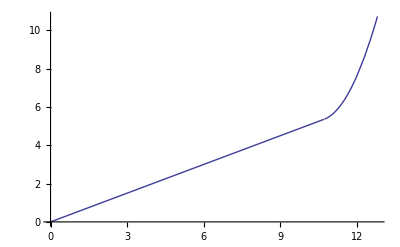

```mathematica
DriftTime[x_]:=Piecewise[{{x/2,x<10.7212},{x^2+(1/2-2 10.7212)x+(10.7212)^2,x≥  10.7212}}]
Plot[DriftTime[x],{x,0,12.8}]
```

### General

```mathematica
Crystal[mwdc_]:=Switch[mwdc,
(*1,{942.86,0,-1400},*)
1,{942.86,0,-946.87},
2,{180,0,-946.87}
]
Rayn[mwdc_,θ_]:={(-1)^mwdc Cos[(θ +30)°],0,Sin[(θ +30)°]}(* Ray vector in mwdc frame, θ = lab angle *)
Ray[mwdc_,θ_,s_]:=Crystal[mwdc]+s Rayn[mwdc,θ]
PayOnMWDC[mwdc_,θ_]:={
Ray[mwdc,θ,s/.Flatten[Solve[Ray[mwdc,θ,s][[3]]==0,s],1]][[1]],
0,
Ray[mwdc,θ,s/.Flatten[Solve[Ray[mwdc,θ,s][[3]]==80,s],1]][[1]],
0} (* the ray of L in k by lab angle *) (* X1, Y1, X2, Y2 *)
LabAngleShift[mwdc_]:=Switch[mwdc,
1,-30,
2,150
]
LabAngle [mwdc_,plan_,wire_](*right-low corner, wire, left-up corner*):={LabAngleShift[mwdc]+(-1)^(mwdc+1)ArcCos[Normalize[(-(wstart[plan,wire]+{-10,0,-8})+Crystal[mwdc])].{1,0,0}]*180/π, (* corner *)
LabAngleShift[mwdc]+(-1)^(mwdc+1)ArcCos[Normalize[(-(wstart[plan,wire])+Crystal[mwdc])].{1,0,0}]*180/π, (* wire *)LabAngleShift[mwdc]+(-1)^(mwdc+1)ArcCos[Normalize[(-(wstart[plan,wire]+{10,0,8})+Crystal[mwdc])].{1,0,0}]*180/π} (* corner *)
MidkX1X2[mwdc_,wire_]:=PayOnMWDC[mwdc,LabAngleShift[mwdc]+(-1)^(mwdc+1)ArcCos[Normalize[(-(wstart[1,wire]+{10,0,0})+CrystalL)].{1,0,0}]*180/π]
DriftX1X2[mwdc_,wire_]:={Abs[DriftLen[MidkX1X2[mwdc,wire],1,wire][[3]]],Abs[DriftLen[MidkX1X2[mwdc,wire],2,wire][[3]]]}
X1X2cell[mwdc_,cell_,shiftAngle_,id1_,id2_]:=MWDC3[
PayOnMWDC[mwdc,LabAngle[mwdc,1,cell][[id1]]-shiftAngle],PayOnMWDC[mwdc,LabAngle[mwdc,2,cell][[id2]]],500,0.2,1]
X1X2[mwdc_,wire_,color_]:=ListPlot[
Table[
k=PayOnMWDC[mwdc,i];
{DriftTime[Abs[DriftLen[k,1,wire][[3]]]],DriftTime[Abs[DriftLen[k,2,wire][[3]]]]},{i,LabAngle[mwdc,If[mwdc==1,2,1],wire][[If[mwdc==1,1,3]]],LabAngle[mwdc,If[mwdc==1,1,2],wire][[If[mwdc==1,3,1]]],0.02}]
,Joined->True,PlotRange->{{0,10.7},{0,10.7}},AspectRatio->1,PlotStyle->color]
X1X1p[mwdc_,wire_,color_]:=ListPlot[
Table[
k=PayOnMWDC[mwdc,i];
{DriftTime[Abs[DriftLen[k,1,wire][[3]]]],DriftTime[Abs[DriftLen[k,1,wire+1][[3]]]]},{i,LabAngle[mwdc,1,wire+1][[1]],LabAngle[mwdc,1,wire][[3]],0.01}]
,Joined->True,PlotRange->{{0,10.7},{0,10.7}},AspectRatio->1,PlotStyle->color]
X1pX2[mwdc_,wire_,color_]:=ListPlot[
Table[
k=PayOnMWDC[mwdc,i];
{DriftTime[Abs[DriftLen[k,1,wire+1][[3]]]],DriftTime[Abs[DriftLen[k,2,wire][[3]]]]},{i,LabAngle[mwdc,1,If[mwdc==1,wire,wire+1]][[1]],LabAngle[mwdc,2,If[mwdc==1,wire+1,wire]][[3]],0.01}]
,Joined->True,PlotRange->{{0,10.7},{0,10.7}},AspectRatio->1,PlotStyle->color]
(* the X2 Drift Len when X1 hit wire *)
AutoX1X2[mwdc_,cell_]:=DriftLen[PayOnMWDC[mwdc,LabAngle[mwdc,1,cell][[1]]-shift],2,cell][[3]]/.FindRoot[DriftLen[PayOnMWDC[mwdc,LabAngle[mwdc,1,cell][[1]]-shift],1,cell][[3]],{shift,0,1}]
```

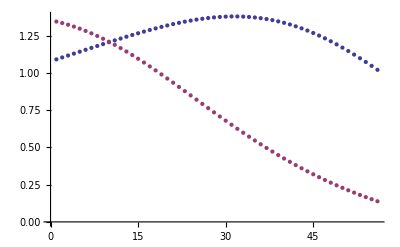

```mathematica
ListPlot[{
Table[LabAngle[1,1,i][[3]]-LabAngle[1,1,i][[1]],{i,56}],
Table[LabAngle[2,1,i][[1]]-LabAngle[2,1,i][[3]],{i,56}]}]
```

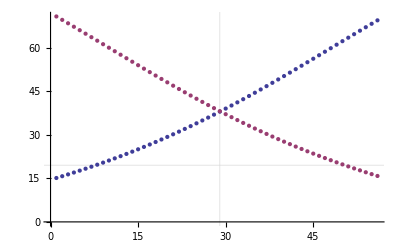

```mathematica
ListPlot[{
Table[LabAngle[1,1,n][[2]],{n,1,56}],
Table[LabAngle[2,1,n][[2]],{n,1,56}]
},GridLines->{{29},{19.54}}]
```

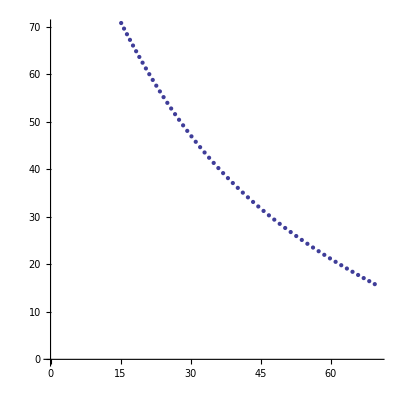

```mathematica
ListPlot[
Table[{LabAngle[1,1,n][[2]],LabAngle[2,1,n][[2]]},{n,1,56}]
,AspectRatio->1,PlotRange->{{0,70},{0,70}}]
```

```mathematica
LabAngle[2,1,23]
LabAngle[2,1,23][[1]]-LabAngle[2,1,23][[3]]
LabAngle[1,1,32][[3]]-LabAngle[1,1,29][[1]]
```

{45.0894,44.6456,44.2112}

0.878234

4.56513

```mathematica
Norm[Pray[PayOnMWDC[1,1],0]-Crystal[1]]
```

1838.45

### L - MWDC

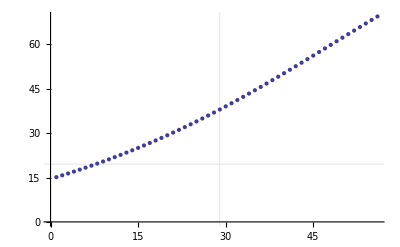

```mathematica
(* incident angle *)
ListPlot[Table[LabAngle[1,1,n][[2]],{n,1,56}],GridLines->{{29},{19.54}}]
```

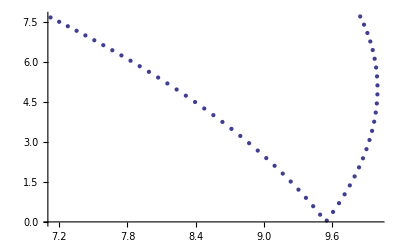

```mathematica
ListPlot[Table[DriftX1X2[1,i],{i,1,56}]]
```

```mathematica
yintL=Table[{n,AutoX1X2[1,n]},{n,4,56,4}];
YintL=Interpolation[Abs[yintL]];
```

```mathematica
(* experiment data *)
expdataL={
{36,40+130},
{40,20+130},
{45,-10+130},
{47,-25+130},
{50,-50+130}};
expdataLint=Interpolation[expdataL];
```

```mathematica
FindRoot[YintL[x]-YintL[40]/expdataLint[40],{x,20,40}]
```

{x→40.}

```mathematica
YintL[40]/expdataLint[40]
```

0.0460767

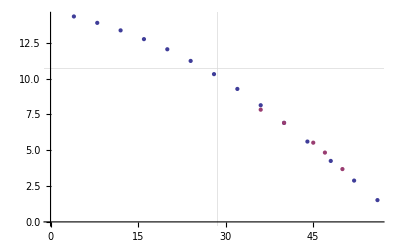

```mathematica
ListPlot[{Abs[yintL],Table[{expdataL[[i,1]],YintL[40]/expdataLint[40] expdataL[[i,2]]},{i,1,5}]},Joined->False, GridLines->{{28.6},{10.7}}]
```

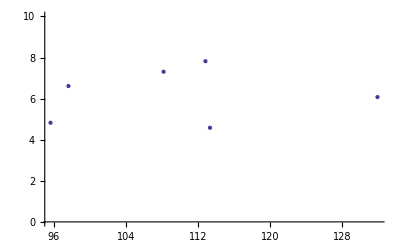

```mathematica
ListPlot[{{113.325836,4.58178473},
{112.81945,7.82204676},
{131.892899,6.07624245},
{95.6432343 ,4.82638407},
{108.177414,7.31052971},
{97.6288223,6.61257029}},PlotRange->{0,10}]
```

### Plot

```mathematica
LabAngle[1,1,33][[2]]
60-LabAngle[1,1,33][[2]]
X1X2cell[1,33,0,2,2]
```

42.2629

17.7371

-Graphics-

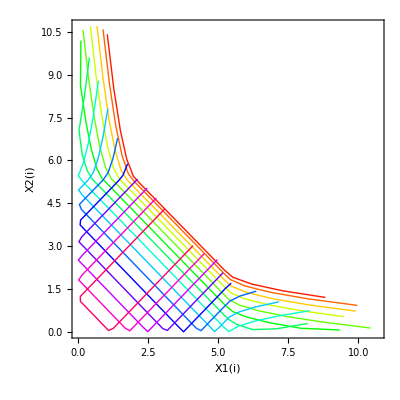

```mathematica
Show[Table[X1X2[1,i,Hue[i/60]],{i,{1, 4,8,12,16,20,24,28,32,36,40,44,48,52,56}}],Frame->True,FrameLabel->{"X1(i)","X2(i)"}]
```

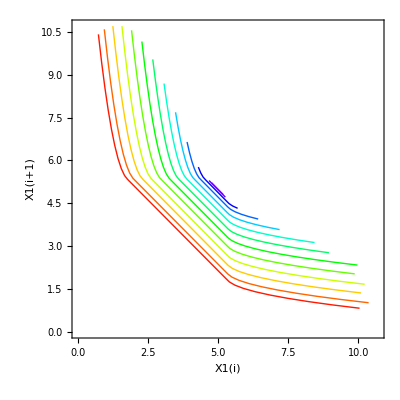

```mathematica
Show[Table[X1X1p[1,i,Hue[i/60]],{i,{1,4,8,12,16,20,24,28,32,36,40,44,45}}],Frame->True,FrameLabel->{"X1(i)","X1(i+1)"}]
```

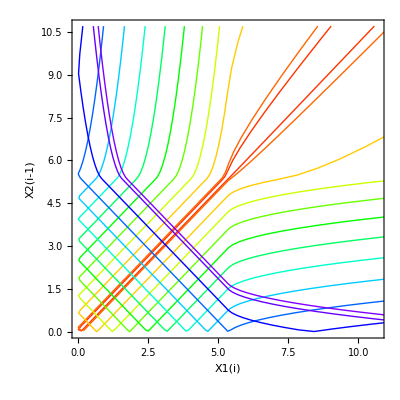

```mathematica
Show[Table[X1pX2[1,i,Hue[i/60]],{i,{2,4,8,12,16,20,24,28,32,36,40,44,45}}],Frame->True,FrameLabel->{"X1(i)","X2(i-1)"}]
```

### MWDC - R

```mathematica
LabAngle[2,1,10][[2]]
60-LabAngle[2,1,10][[2]]
X1X2cell[2,10,0,2,2]
```

60.

0.

-Graphics-

```mathematica
yintR=Table[{n,RAutoX1X2[n]},{n,1,56,1}];
```

```mathematica
Sort[Abs[yintR],#1[[2]]>#2[[2]]&][[-1]]
```

{25,0.0660956}

```mathematica
yintRdata=Map[#-{0,-130}&,{
{5,0},
{8,-25},
{12,-50},
{15,-60},
{20,-105},
{22,-110},
{28,-110},
{31,-90},
{32,-82},
{37,-60},
{39,-45},
{43,-30},
{47,-20},
{49,-10},
{52,0},
{56,20}}];
```

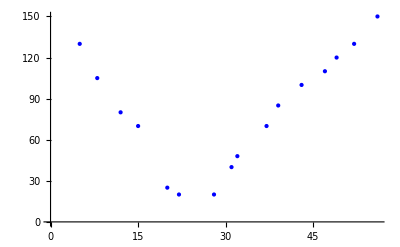

```mathematica
ListPlot[yintRdata,PlotStyle->{ Blue}]
```

```mathematica
yintR[[43,2]]/yintRdata[[12,2]]
```

0.0504738

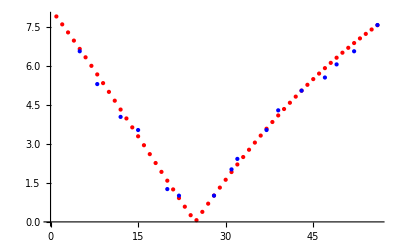

```mathematica
ListPlot[{Abs[yintR],Map[#*{1,yintR[[43,2]]/yintRdata[[12,2]]}&,yintRdata]},PlotStyle->{Red, Blue}]
```

### Plot

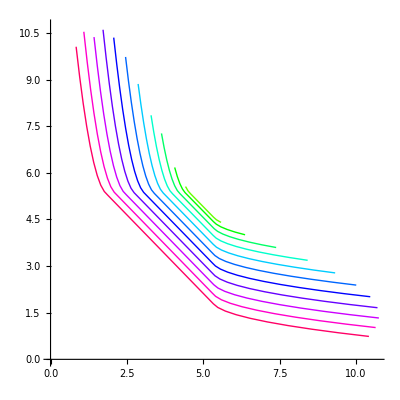

```mathematica
Show[Table[X1X1p[2,i,Hue[i/60]],{i,{16,20,24,28,32,36,40,44,48,52,56}}]]
```

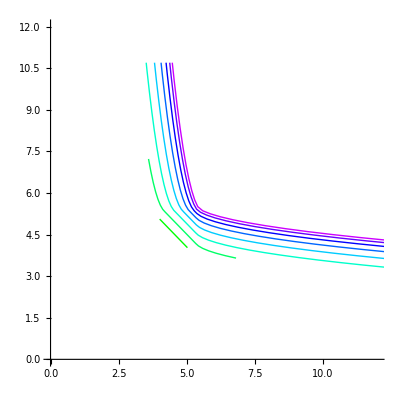

```mathematica
Show[Table[X1pX2[2,i,Hue[i/60]],{i,{20,24,28,32,36,40,44,48}}],PlotRange->{{0,12},{0,12}}]
```

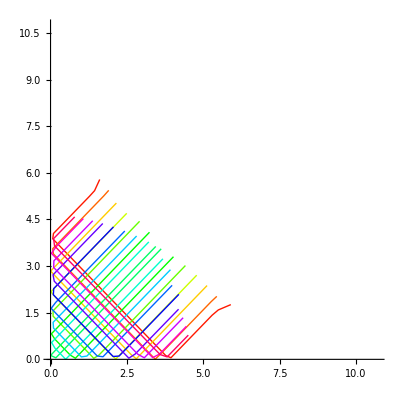

```mathematica
Show[Table[X1X2[2,i,Hue[i/60]],{i,{1,4,8,12,16,20,24,28,32,36,40,44,48,52,56}}]]
```

## PP elastics

```mathematica
mp=938.27203;
T1[T_,α_ ]:=T Cos[α °/2]^2
T2[T_,α_]:=T Sin[α °/2]^2
θ1[T_,α_(* deg *)](* deg *):=ArcTan[Sqrt[T (2 mp+T)] Cos[α °/2]^2,(Sqrt[mp T] Sin[α °])/Sqrt[2]] 180/π
θ2[T_,α_(* deg *)](* deg *):=ArcTan[Sqrt[T (2 mp+T)] Sin[α °/2]^2,-((Sqrt[mp T] Sin[α °])/Sqrt[2])] 180/π
Einc[m_,ToF_ (*ns *),l_]:=With[{c=0.299792458},(m (c ToF √(c^2 ToF^2-l^2)-(c^2 ToF^2-l^2)))/(c^2 ToF^2-l^2)]
ToF[m_,Ein_,l_]:=With[{c=299792458},(l(m+Ein))/(c √(2m Ein+Ein^2))10^9](*ns*)
```

```mathematica
flL[α_]:=Norm[Pray[PayOnMWDC[1,θ1[260,α]],400]-Crystal[1]] (* flight lenght [mm] *)
ToFTplL[α_]:=(flL[α](mp +T1[260,α]))/(299792458 √(2mp T1[260,α]+T1[260,α]^2))10^6 (* ns *)
flR[α_]:=Norm[Pray[PayOnMWDC[2,-θ2[260,α]],400]-Crystal[2]] (* flight lenght *)
ToFTplR[α_]:=(flR[α](mp +T2[260,α]))/(299792458 √(2mp T2[260,α]+T2[260,α]^2))10^6 (* ns *)
```

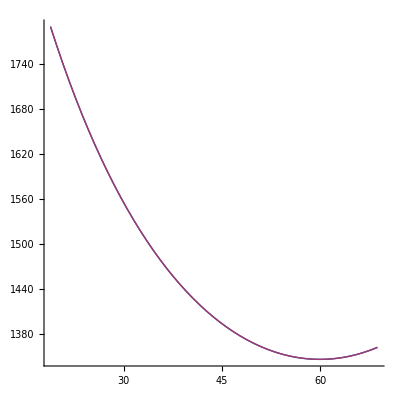

```mathematica
ParametricPlot[{{θ1[260,α],(-Crystal[1][[3]]+400)/Cos[π/3-θ1[260,α] π/180]},{θ1[260,α],flL[α]}},{α,40,140},PlotRange->{{20,70},{0,All}},AspectRatio->1]
```

```mathematica
(* Given Lab angle and find the ToF *)
FindRoot[θ1[260,α1]==70,{α1,50}]
ToFTplL[α1]/.%
```

{α1→142.33}

16.5108

```mathematica
(* Given ToF and find the lab angle *)
FindRoot[ToFTplL[α1]==8,{α1,100}]
θ1[260,α1]/.%
```

{α1→74.689}

35.5682

```mathematica
tplSH={
{21,-178},
{30,-180},
{40,-181.8},
{50,-183.1},
{60,-184.8}};
```

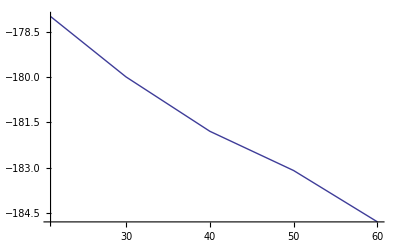

```mathematica
ListPlot[tplSH,Joined->True]
```

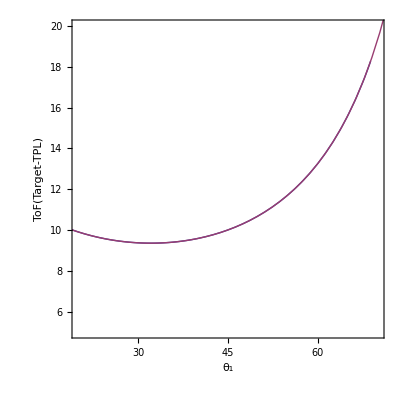

```mathematica
ParametricPlot[{{θ1[260,α],ToFTplL[α]},{-θ2[260,α],ToFTplR[α]}},{α,20,140},AspectRatio-> 1, PlotRange-> {{20,70},{5, 20}},Frame->True, FrameLabel-> {"θ_1","ToF(Target-TPL)"}]
```

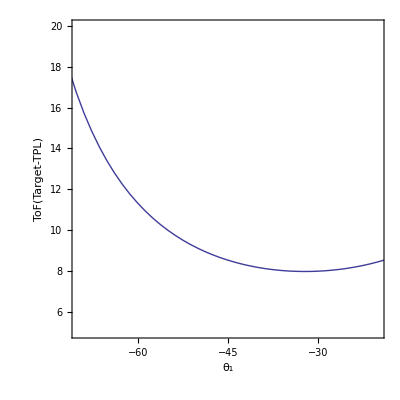

```mathematica
ParametricPlot[{{θ2[260,α],ToFTplR[α]}},{α,20,140},AspectRatio-> 1, PlotRange-> {{-70,-20},{5, 20}},Frame->True, FrameLabel-> {"θ_1","ToF(Target-TPL)"}]
```

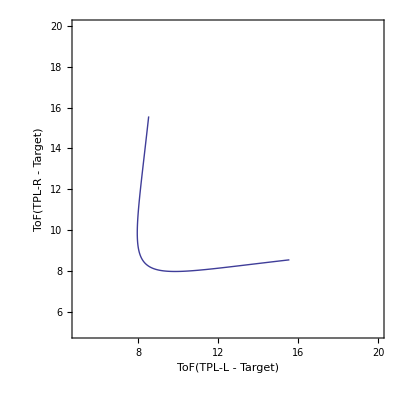

```mathematica
ParametricPlot[{ToFTplL[α],ToFTplR[α]},{α,40,140},AspectRatio-> 1, PlotRange-> {{5,20},{5, 20}},Frame->True, FrameLabel-> {"ToF(TPL-L - Target)","ToF(TPL-R - Target)"}]
```

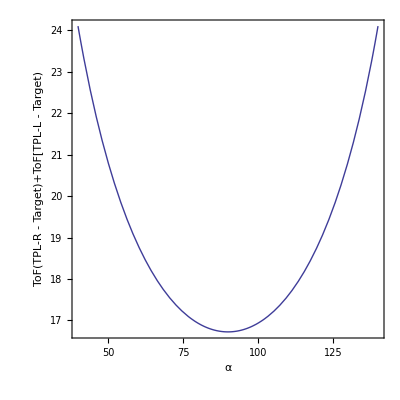

```mathematica
Plot[ToFTplL[α]+ToFTplR[α],{α,40,140},AspectRatio-> 1, Frame->True, FrameLabel-> {"α","ToF(TPL-R - Target)+ToF[TPL-L - Target)"}]
```

```mathematica
(* Timing of Plastics *)
```

```mathematica
F3[t_]:=Sum[Exp[-i/10]UnitBox[t-27 i],{i,0,10}]
FH9[t_]:=Sum[Exp[-i/10]UnitBox[t-27 i-394.574],{i,0,10}]
Tgt[t_]:=Sum[Exp[-i/10]UnitBox[t-27 i-451.7844],{i,0,10}]
SO[t_]:=Sum[Exp[-i/10]UnitBox[t-27 i-463.046],{i,0,10}]
timingTpl=Table[ToFTplL[RandomReal[{42,142}]],{i,0,10}];
PLL[t_]:=Sum[Exp[-i/10]UnitBox[t-27 i-451.7844-timingTpl[[i+1]]],{i,0,10}]
```

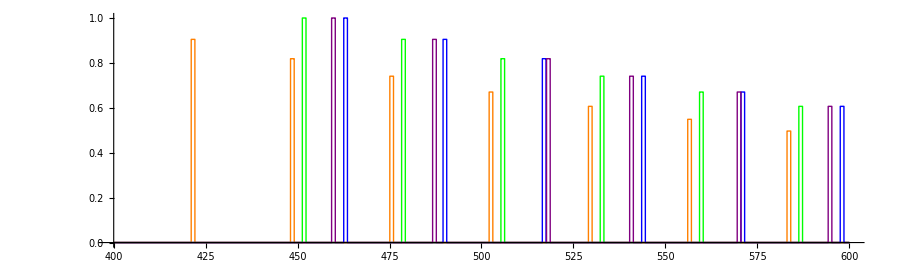

```mathematica
Plot[{F3[t],FH9[t],Tgt[t],SO[t],PLL[t]},{t,400,600},PlotPoints->400,AspectRatio->0.3,ImageSize->900,PlotStyle->{ Red,Orange, Green, Blue,Purple}]
```

```mathematica
θ1[260,90 ]
PayOnMWDC[1,θ1[260,90]]
HitList[PayOnMWDC[1,θ1[260,90]]][[1,2]]
```

43.1427

{655.949,0,631.708,0}

34

```mathematica
MWDC3[PayOnMWDC[1,θ1[260,90 ]],PayOnMWDC[1,θ1[260,91 ]],500, 0.1,1]
```

-Graphics-

```mathematica
MWDC3[PayOnMWDC[2,-θ2[260,90 ]],PayOnMWDC[2,-θ2[260,91 ]],500, 0.1,1]
```

-Graphics-

```mathematica
(* simulate MWDC L R ID *)
```

```mathematica
{HitList[PayOnMWDC[1,θ1[260,36]]][[1,2]],HitList[PayOnMWDC[2,-θ2[260,36]]][[1,2]]}
{HitList[PayOnMWDC[1,θ1[260,142]]][[1,2]],HitList[PayOnMWDC[2,-θ2[260,142]]][[1,2]]}
```

{4,1}

{56,53}

```mathematica
hist=Table[{HitList[PayOnMWDC[1,θ1[260,α]]][[1,2]],HitList[PayOnMWDC[2,-θ2[260,α]]][[1,2]]},{α,36,140,0.1}];
```

```mathematica
HistogramList[Transpose[hist][[1]],56]
```

{{4.,5.,6.,7.,8.,9.,10.,11.,12.,13.,14.,15.,16.,17.,18.,19.,20.,21.,22.,23.,24.,25.,26.,27.,28.,29.,30.,31.,32.,33.,34.,35.,36.,37.,38.,39.,40.,41.,42.,43.,44.,45.,46.,47.,48.,49.,50.,51.,52.,53.,54.,55.,56.},{11,14,14,15,14,16,15,15,16,17,16,17,17,18,17,18,19,19,19,19,20,19,21,20,21,21,21,22,21,22,23,22,23,22,23,23,23,24,23,23,24,23,24,23,24,23,23,23,23,23,23,22}}

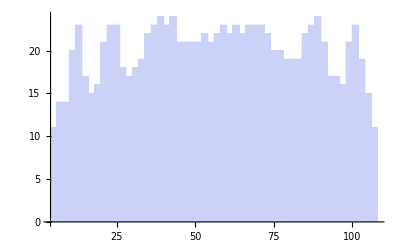

```mathematica
Histogram[Map[Total[#1]&,hist,{1}],56]
```

```mathematica
hist[[1]]
```

{4,1}

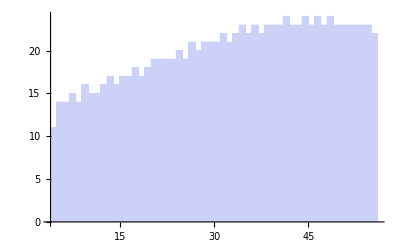

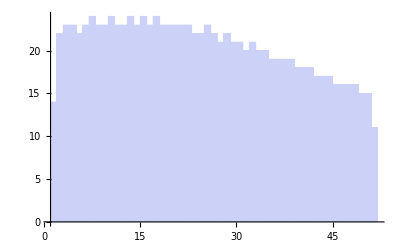

```mathematica
Histogram[Transpose[hist][[1]],56]
Histogram[Transpose[hist][[2]],56]
```

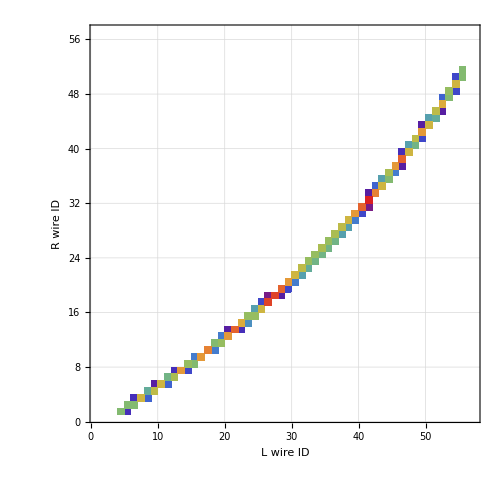

```mathematica
DensityHistogram[hist,56,GridLines->Automatic,PlotRange->{{1,57},{1,57}},ImageSize->500,Frame-> True,FrameLabel->{"L wire ID","R wire ID"},ColorFunction->"Rainbow"]
```

```mathematica
{PayOnMWDC[1,θ1[260,36]][[1]],PayOnMWDC[2,-θ2[260,36]][[1]]}
{PayOnMWDC[1,θ1[260,140]][[1]],PayOnMWDC[2,-θ2[260,140]][[1]]}
```

{57.9082,-1.97202}

{1089.03,1007.91}

```mathematica
histXLR=Table[{PayOnMWDC[1,θ1[260,α]][[1]],PayOnMWDC[2,-θ2[260,α]][[1]]},{α,36,140,0.1}];
```

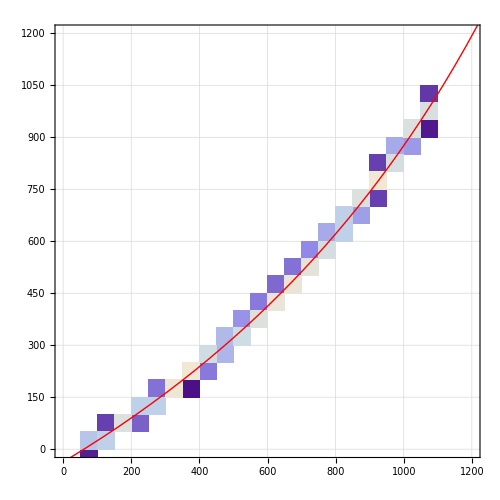

```mathematica
Show[DensityHistogram[histXLR,20,GridLines->Automatic,PlotRange->{{0,1200},{0,1200}},ImageSize->500],
ParametricPlot[{PayOnMWDC[1,θ1[260,α]][[1]],PayOnMWDC[2,-θ2[260,α]][[1]]},{α,0,180},PlotStyle->Red]]
```